# Wolfram language symbol relations

## Dump Data:

```mathematica
DocCellDump=Flatten[Import/@FileNames["*","C:\\Users\\dell\\Downloads\\SymbolLists\\SymbolLists\\"],1];
 DocCellDump=DeleteCases[DeleteCases[DocCellDump,_getSymbols],{}];
CleanedDump=DeleteCases[Flatten@DocCellDump,_getSymbols];
SymbolFreq=Counts@CleanedDump;
SymbolNames=Keys[SymbolFreq];
filteredFunctionSet=Select[Tally[Sort[Sort/@Join@@(Subsets[DeleteDuplicates[#],{2}]&/@DocCellDump)]],FreeQ[#,"List"|"Rule"|"Set"|"Null"|"SetDelayed"|"Power"|"Plus"|"All"|"Automatic"|"Times"|"RuleDelayed"|"True"|"False"|"CompoundExpression"|"Slot"]&];
functionSet=Select[Tally[Sort[Sort/@Join@@(Subsets[DeleteDuplicates[#],{2}]&/@DocCellDump)]],FreeQ[#,""]&];
```

## Define Functions:

```mathematica
MutualFunctionUse[sym1_,sym2_,functset_]:=
Cases[functset,{{sym1,If[sym2=="",_String,sym2]},_Integer}]
functiongather[funct1_,functset_,n_]:=
MaximalBy[MutualFunctionUse[funct1,"",functset],Last,UpTo[n]]
functionGraph[x_,n_,functset_]:=
Module[{edges,edgelabels,sizes,mutualfunctions,graph,finished},
mutualfunctions=functiongather[x,functset,n];
edges=Thread[mutualfunctions⟦1;;,1,1⟧<->mutualfunctions⟦1;;,1,2⟧];
edgelabels= Thread[Thread[mutualfunctions⟦1;;,1,1⟧<->mutualfunctions⟦1;;,1,2⟧]->mutualfunctions⟦1;;,2⟧];
finished=Thread[Part[edgelabels,All,1]->Evaluate@(Placed[#,Tooltip]&/@ (Part[edgelabels,All,2]))];
sizes=Append[Thread[Evaluate@mutualfunctions⟦1;;,1,2⟧->(#*0.1&)/@Floor/@Log/@Evaluate@(SymbolFreq[#]&/@mutualfunctions⟦1;;,1,2⟧)],x->0.1*Floor@Log@SymbolFreq[x]];

graph=Graph[edges,VertexLabels->Placed["Name",Center],VertexSize->sizes,EdgeLabels->finished,Background->White,ImageSize->Full,EdgeWeight->Flatten@mutualfunctions⟦All,2⟧];
{CommunityGraphPlot[graph],MatrixPlot[WeightedAdjacencyMatrix[graph]]}

 ]
allfunctionGraph[x_,functset_,n_]:=
Module[{edges,edgelabels,sizes,mutualfunctions,graph,finished},
mutualfunctions=functiongather[#,functset,n]&/@x;
edges=Thread[Flatten@mutualfunctions⟦All,All,1,1⟧<->Flatten@mutualfunctions⟦All,All,1,2⟧];
edgelabels= Thread[Thread[(Flatten@mutualfunctions⟦All,All,1,1⟧<->Flatten@mutualfunctions⟦All,All,1,2⟧)]->Flatten@mutualfunctions⟦All,All,2⟧];
finished=Thread[Part[edgelabels,All,1]->Evaluate@(Placed[#,Tooltip]&/@ (Part[edgelabels,All,2]))];
sizes=Append[Thread[Evaluate@Flatten@mutualfunctions⟦All,All,1,2⟧->(#*0.1&)/@Floor/@Log/@Evaluate@(SymbolFreq[#]&/@Flatten@mutualfunctions⟦All,All,1,2⟧)],Thread[x->0.1*Floor/@(Log/@(SymbolFreq/@x))]];
graph=Graph[edges,VertexLabels->Placed["Name",Tooltip],VertexSize->sizes,EdgeLabels->finished,Background->White,ImageSize->Full,EdgeWeight->Flatten@mutualfunctions⟦All,All,2⟧];
{CommunityGraphPlot[graph],MatrixPlot[WeightedAdjacencyMatrix[graph],ImageSize->Full]}
 ]
SimpleAllFunctionGraph[x_,functset_,n_]:=
Module[{edges,edgelabels,sizes,mutualfunctions,graph},
mutualfunctions=functiongather[#,functset,n]&/@x;
edges=Thread[Flatten@mutualfunctions⟦All,All,1,1⟧<->Flatten@mutualfunctions⟦All,All,1,2⟧];
sizes=Append[Thread[Evaluate@Flatten@mutualfunctions⟦All,All,1,2⟧->(#*0.1&)/@Floor/@Log/@Evaluate@(SymbolFreq[#]&/@Flatten@mutualfunctions⟦All,All,1,2⟧)],Thread[x->0.1*Floor/@(Log/@(SymbolFreq/@x))]];

graph=Graph[edges,VertexLabels->Placed["Name",Tooltip],Background->White,ImageSize->Full];
CommunityGraphPlot[graph]
 ]
functionbarPlot[funct_,functset_,n_]:=
Module[{data},
data=functiongather[funct,functset,n];
BarChart[N/@Thread[Divide[data⟦All,2⟧,SymbolFreq[#]&/@data⟦All,1,2⟧]],ChartLabels->data⟦All,1,2⟧,ImageSize->Full]
]
```

## Visualizing the data

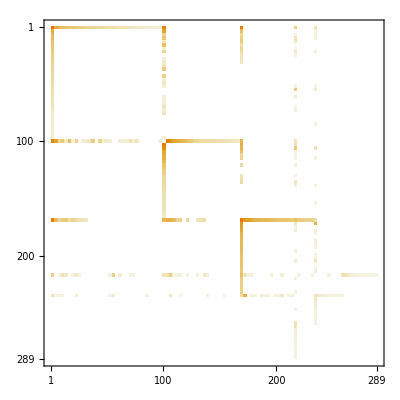
{-Graphics-,-Graphics-}

```mathematica
allfunctionGraph[{"Sin","Plot","Cos","DSolve","NDSolve"},filteredFunctionSet,100]
```

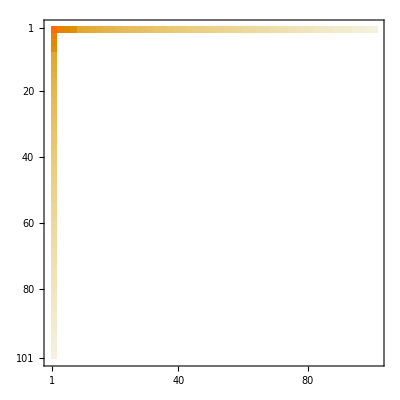
{-Graphics-,-Graphics-}

```mathematica
functionGraph["List",100,functionSet]
```

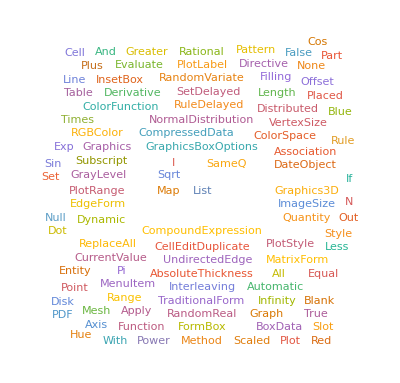

```mathematica
WordCloud[CleanedDump,ImageSize->Full]
```

```mathematica
SimpleAllFunctionGraph[{"Cos","Sin","Tan","Cot","Sec","Csc","Tanh","Cosh","Sinh"},filteredFunctionSet,10]
```

-Graphics-

```mathematica
SimpleAllFunctionGraph[SymbolNames,filteredFunctionSet,10]
```

-Graphics-

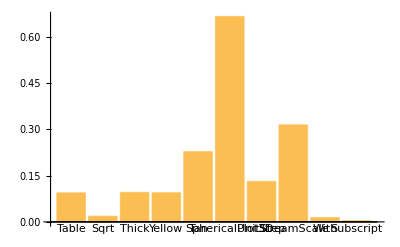

```mathematica
functionbarPlot["Sin",filteredFunctionSet,10]
```